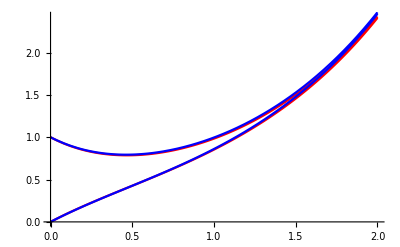

```mathematica
(*X={xi,yi}*)
exactSol[t_]={x[t],y[t]}/.DSolve[{x'[t]==2y[t]-x[t],y'[t] == x[t], x[0]==1, y[0]==0},{x[t],y[t]},t][[1]];
F1[t_, X_]:={
2X[[2]]-X[[1]],
X[[1]]
};
t0 = {1,0};
EulerForward[du_, du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret, tcurr},

t=Subdivide[t0,T,n];
h = (T-t0)/n;

y= Table[0, Length[t]];

y[[1]] = du0;
tcurr = t0;

For[i = 2, i≤ Length[t], i++,
y[[i]] = N[y[[i-1]]+h*(du[t0,y[[i-1]]])];
tcurr = tcurr+h;
];

ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]
]
res = EulerForward[F1,t0,0,2,100];
res2   = Table[Table[{res[[j,1]], res[[j,2,i]]},{j,1, Length[res]}], {i,1,2}];
Show[{
ListLinePlot[res2, PlotStyle->Red],
Plot[exactSol[t],{t,0,2},PlotStyle->Blue]
}]
```

```mathematica
RK4[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3,k4,tcurr,tarr},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;
tarr = Table[0,n];
tarr[[1]]=t;
tcurr = t+h;

For[i=2, i≤n,i++,
k1 = h*du[tcurr, y[[i-1]]]//N;
k2 = h*du[tcurr+1/2 h, y[[i-1]]+1/2 k1]//N;
k3=h*du[tcurr+1/2 h, y[[i-1]]+1/2 k2]//N;
k4 = h*du[tcurr+2/3 h,y[[i-1]]+k3]//N;
tcurr = tcurr+h;
tarr[[i]] = tcurr;
y[[i]]=y[[i-1]]+(1/6 k1+1/3 k2+1/3 k3+1/6 k4)//N; 
];

ret = Table[{tarr[[i]], y[[i]]}, {i,1,n}]
];
AB[du_,u0_,t_,T_,h_]:=Module[
{ycurr,n,len,y,i},

n =Floor[ (T-t)/h];
ycurr =RK4[du,u0,t,t+4h,h];
len = 4;

For[i = len, i≤n,i++,
y =ycurr[[i,2]]+1/24 h (
55 du[ycurr[[i,1]],ycurr[[i,2]]]
-9 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]
+37 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]
-59 du[ycurr[[i-1,1]],ycurr[[i-1,2]]]);

AppendTo[ycurr, {ycurr[[i,1]]+h,y }];

];
Return[ycurr];
]
F2[t_, X_]:={
X[[2]],
9.8-1X[[1]]
}
```

```mathematica
res3 = AB[F2, {0,0},0,10,0.1];
res4 = Table[res3[[i,2,2]],{i,1,Length[res3]}];
ballSpring[posY_,posX_]:={Circle[{posX,-posY},0.5],Line[{{posX,-posY},{posX,0}}]}
Animate[Graphics[{ballSpring[res4[[i]],5.5],Red},PlotRange->{{0,10},{-22,0}}],{i,1,Length[res4],1}]
```

```mathematica
f[t_, u_]:=10^6(-u+Sin[t]);
RK4[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3,k4,tcurr,tarr},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;
tarr = Table[0,n];
tarr[[1]]=t;
tcurr = t+h;

For[i=2, i≤n,i++,
k1 = h*du[tcurr, y[[i-1]]]//N;
k2 = h*du[tcurr+1/2 h, y[[i-1]]+1/2 k1]//N;
k3=h*du[tcurr+1/2 h, y[[i-1]]+1/2 k2]//N;
k4 = h*du[tcurr+2/3 h,y[[i-1]]+k3]//N;
tcurr = tcurr+h;
tarr[[i]] = tcurr;
y[[i]]=y[[i-1]]+(1/6 k1+1/3 k2+1/3 k3+1/6 k4)//N; 
];

ret = Table[{tarr[[i]], y[[i]]}, {i,1,n}]
];
EulerForward[du_, du0_, t0_, T_, h_]:=Module[
{t, y, i, ret, tcurr,n},

n = Floor[(T-t0)/h];
t=Subdivide[t0,T,n];

y= Table[0, n];

y[[1]] = du0;

tcurr = t0 + h;

For[i = 2, i< n, i++,
y[[i]] = y[[i-1]]+h(du[tcurr,y[[i-1]]]);
tcurr = tcurr+h;
];

ret = Table[{t[[i]], y[[i]]}, {i,1,n}]//N
]
EulerBackwardsV1[du_,du0_, t0_, T_, h_]:=Module[
{t, y, i, ret, aprY,n},

n = Floor[ (T-t0)/h];
aprY = EulerForward[du,du0, t0, T, h];


t=Subdivide[t0,T,n];


y= Table[0, n];
y[[1]] = du0;

For[i = 1, i<n, i++,
y[[i+1]] =fy/.FindRoot[fy == y[[i]]+h*du[t[[i]],fy], {fy, aprY[[i+1,2]]}]
];
ret = Table[{t[[i]], y[[i]]}, {i,1,n}]

]
```

ListLinePlot::prng: Value of option PlotRange -> {{0,10.},{-4.81228967421683×10^1209,0.999574}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

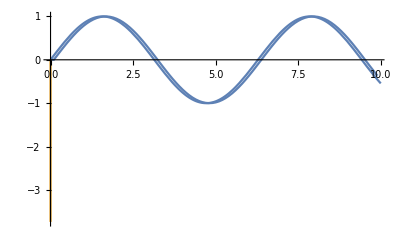

```mathematica
Show[{
ListLinePlot[{EulerBackwardsV1[f,0,0,10, 0.1], RK4[f,0,0,10, 0.1]}],
Plot[exactSol2[t], {t,0,10},PlotRange->All]

}]
```

```mathematica
|
```

```mathematica
RK4[f,0,0,10, 0.001]
```

{{0,0},{0.002,-4.1459×10^7},{0.003,-1.72057×10^18},9995,{9.999,-1.97991104350281×10^106156},{10.,-8.21672962829572×10^106166}}
 |  |  |  |

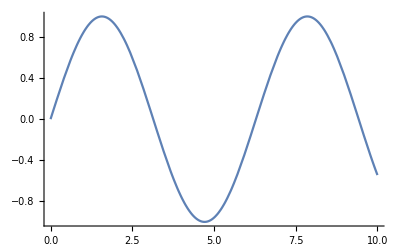

```mathematica
Plot[exactSol2[t], {t,0,10},PlotRange->All]
```

```mathematica
exactSol2[t]//Simplify
```

(1000000 (ⅇ^(-1000000 t)-Cos[t]+1000000 Sin[t]))/1000000000001

```mathematica
exactSol2[t_]=u[t]/.DSolve[{u'[t]==10^6(-u[t]+Sin[t]),u[0]==0},u[t],t][[1]]//Simplify;
```

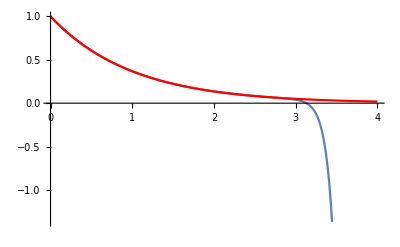

```mathematica
F3[t_,X_]:={
X[[2]],
10X[[2]]+11X[[1]]
}
RK4[du_,du0_, t_,T_, h_]:=Module[
{alphas,betas, p,n,y, i,k1,k2,k3,k4,tcurr,tarr},

n = Floor[(T-t)/h];

y= Table[0, n];
y[[1]]=du0;
tarr = Table[0,n];
tarr[[1]]=t;
tcurr = t+h;

For[i=2, i≤n,i++,
k1 = h*du[tcurr, y[[i-1]]]//N;
k2 = h*du[tcurr+1/2 h, y[[i-1]]+1/2 k1]//N;
k3=h*du[tcurr+1/2 h, y[[i-1]]+1/2 k2]//N;
k4 = h*du[tcurr+2/3 h,y[[i-1]]+k3]//N;
tcurr = tcurr+h;
tarr[[i]] = tcurr;
y[[i]]=y[[i-1]]+(1/6 k1+1/3 k2+1/3 k3+1/6 k4)//N; 
];

ret = Table[{tarr[[i]], y[[i]]}, {i,1,n}]
];
AB[du_,u0_,t_,T_,h_]:=Module[
{ycurr,n,len,y,i},

n =Floor[ (T-t)/h];
ycurr =RK4[du,u0,t,t+4h,h];
len = 4;

For[i = len, i≤n,i++,
y =ycurr[[i,2]]+1/24 h (
55 du[ycurr[[i,1]],ycurr[[i,2]]]
-9 du[ycurr[[i-3,1]],ycurr[[i-3,2]]]
+37 du[ycurr[[i-2,1]],ycurr[[i-2,2]]]
-59 du[ycurr[[i-1,1]],ycurr[[i-1,2]]])//N;

AppendTo[ycurr, {ycurr[[i,1]]+h,y }];

];
Return[ycurr];
]
res5 = AB[F3, {-1,1},0,4,0.001];
res6 = Table[Table[{res5[[j,1]], res5[[j,2,i]]},{j,1, Length[res5]}], {i,2,2}];
Show[{
ListLinePlot[res6],
Plot[E^-t,{t,0,4},PlotStyle->Red]
}]
```

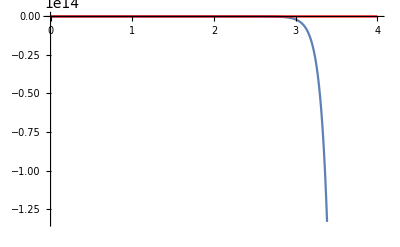

```mathematica
res5 = AB[F3, {-1,0.99},0,4,0.001];
res6 = Table[Table[{res5[[j,1]], res5[[j,2,i]]},{j,1, Length[res5]}], {i,2,2}];
Show[{
ListLinePlot[res6],
Plot[E^-t,{t,0,4},PlotStyle->Red]
}]
```